```mathematica
(* This notebook draws a spiral on top of the graph of y=x^2. *)
```

```mathematica
(* The Nest command can be used to iterate a function. *)
Nest[Sin,1,5]
```

Sin[Sin[Sin[Sin[Sin[1]]]]]

```mathematica
(* The Table command makes lists of numbers *)
squares=Table[n^2,{n,1,20}]
cubes=Table[n^3,{n,1,20}]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

{1,8,27,64,125,216,343,512,729,1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

```mathematica
(* We can use Riffle to alternate elements from two lists. *)
Riffle[squares,cubes]
```

{1,1,4,8,9,27,16,64,25,125,36,216,49,343,64,512,81,729,100,1000,121,1331,144,1728,169,2197,196,2744,225,3375,256,4096,289,4913,324,5832,361,6859,400,8000}

```mathematica
(* Table can also be used to make lists of points *)
Table[{n,n^2},{n,1,20}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100},{11,121},{12,144},{13,169},{14,196},{15,225},{16,256},{17,289},{18,324},{19,361},{20,400}}

{{0.0353553,0.0353553},{0.,0.1},{-0.106066,0.106066},{-0.2,0.},{-0.176777,-0.176777},{0.,-0.3},{0.247487,-0.247487},{0.4,0.},{0.318198,0.318198},{0.,0.5},{-0.388909,0.388909},{-0.6,0.},{-0.459619,-0.459619},{0.,-0.7},{0.53033,-0.53033},{0.8,0.}}

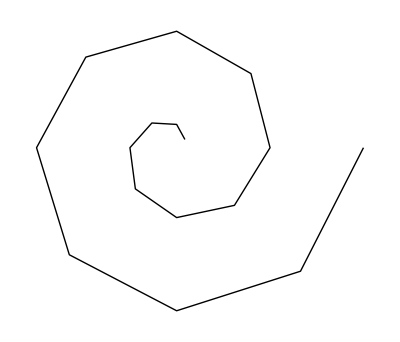

```mathematica
(* The Line and Graphics commands can draw line segments from a list of points *)
spiralpoints=Table[{0.05*n*Cos[n*Pi/4],0.05*n*Sin[n*Pi/4]},{n,1,16}]
spiral=Graphics[Line[spiralpoints]]
```

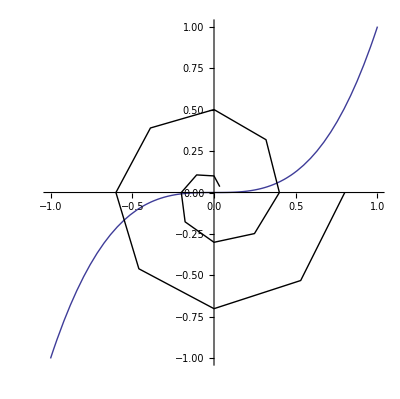

```mathematica
(* We can use Show to superimpose this spiral with a Plot. *)
Show[ Plot[x^3,{x,-1,1},AspectRatio->Automatic], spiral ]
```